## Guitar String

## Completed and Analyzed in class, April 8, 2025

This is our eighteenth notebook. For most of your special projects, the type of work we did in the seventeenth notebook (Harmonic Oscillator Redux) is more relevant than what I am going to show you now. Please keep referring to that notebook. It had everything you need to know about how to put “ordinary differential equations” into Mathematica.

In this notebook, as part of analyzing a guitar string, we going to put what are called “partial differential equations” into Mathematica.

### Guitar String — Theory

Back in the thirteenth notebook titled “Torsion Waves,” we got our first really good visualization of waves. Torsion waves are a good choice because they are more vivid to look at than the transverse waves on a guitar string. Also, an apparatus that is usually purchased by physics departments for wave demonstrations of waves does torsion waves:


But now I am going to switch to guitar strings, and the mathematics is completely equivalent! Here was the angular acceleration formula from the Torsion Waves notebook:

α_j=-ω_0^2(θ_j-θ_(j-1))+ω_0^2(θ_(j+1)-θ_j)

The corresponding guitar string formula would be:

a_j=-ω_0^2(z_j-z_(j-1))+ω_0^2(z_(j+1)-z_j)

In a theory notebook titled “The Second Derivative,” I did some casual hand-waving of the kind physicists are prone to do, and convinced you (I hope) that what we really had in the limit that the chunks and the time steps got smaller and smaller was:

(∂^2 θ)/(∂t^2)=v_0^2(∂^2 θ)/(∂x^2)

For a guitar string, the corresponding equation is:

(∂^2 z)/(∂t^2)=v_0^2(∂^2 z)/(∂x^2)

Let’s be clear about the dependent and independent variables. The time is t. The guitar string is strung along the x-axis. Those are the independent variables. The dependent variable is the displacement, which we are putting in the z-direction, so the dependent variable is z, and we want to find the function of two variables, z(t,x).

### Partial Derivatives and Their Notation

Now that we have two independent variables, we have to clarify for Mathematica which variable we are taking a derivative with respect to. In other words, the obvious generalization of

```mathematica
Derivative[2][z][t] // TraditionalForm
```

z''(t)

which would be

```mathematica
Derivative[2][z][t,x]// TraditionalForm
```

z''(t,x)

is ambiguous. Are we taking the derivative with respect to t or x? Mathematica specifies it this way:

```mathematica
Derivative[2,0][z][t,x]// TraditionalForm
```

z^(2,0)(t,x)

That’s two derivatives with respect to the first variable, t. And here is two derivatives with respect to the second variable, x:

```mathematica
Derivative[0,2][z][t,x]// TraditionalForm
```

z^(0,2)(t,x)

You can even do mixed partial derivatives, such as one derivative with respect to t and one derivative with respect to x, but we have no need for that.

### The Guitar String Differential Equation

Now that we know how the notation for how Mathematica expects us to specify partial differential equations, we can give it this differential equation:

(∂^2 z)/(∂t^2)=v_0^2(∂^2 z)/(∂x^2)

Review the previous notebook to see how that was done in for the harmonic oscillator.

```mathematica
(* Module[{rootin tootin }]
“Well… Afore hoo’d bin here three days hoo’d hauve a dozen colliers whewtin’ an’ tootin’ after her every neet.” *)
```

```mathematica
Module[{v0=1},{Derivative[2,0][z][t,x]==v0^2 Derivative[0,2][z][t,x]}] // TraditionalForm
```

{z^(2,0)(t,x)==z^(0,2)(t,x)}

### Adding the Boundary Conditions

We are missing the boundary conditions on the string at the bridge and the nut of the guitar.

-Graphics-

Put those in:

```mathematica
length=1;

Module[{v0=1},{Derivative[2,0][z][t,x]==v0^2 Derivative[0,2][z][t,x],z[t,0]==0, z[t,length]==0}] // TraditionalForm
```

{z^(2,0)(t,x)==z^(0,2)(t,x),z(t,0)==0,z(t,1)==0}

### Adding the Initial Conditions

We are also missing any specification of the initial motion of the string. It isn’t just going to start vibrating by itself. Here is an initial displacement function:

```mathematica
amplitude=1;
mode=1;

f[x_]:=amplitude Sin[mode Pi x]
```

With mode=1, you have the “fundamental.” With mode=2, you have the “first harmonic.” With mode=3, you have the “second harmonic.” Add f[x] as an initial displacement to the equations. Also add an initial velocity all along the string of 0. Give the resulting problem, which is finally completely specified, a name:

```mathematica
exactGuitarStringProblem=Module[{v0=1},{Derivative[2,0][z][t,x]==v0^2 Derivative[0,2][z][t,x],z[t,0]==0, z[t,length]==0,z[0,x]==f[x],Derivative[1,0][z][0,x]==0}];
```

### Making Mathematica Solve the Guitar String Problem

This problem has an exact solution. So we can use DSolve[] rather than NDSolve[]:

```mathematica
exactGuitarStringSolutionRule=DSolve[exactGuitarStringProblem][[1]]
```

{z[t,x]→Cos[π t] Sin[π x]}

We have the same problems as we had with the harmonic oscillator solution: (1) It is a list of lists of rules, and (2) we haven’t given it a name so don’t have a convenient way of using it elsewhere. Fix these problems:

```mathematica
exactGuitarStringSolutionRule=DSolve[exactGuitarStringProblem][[1]]
```

{z[t,x]→Cos[π t] Sin[π x]}

It is still a rule. Turn it into a function that we can plot:

```mathematica
exactGuitarStringSolution[t_,x_]=z[t,x]/.exactGuitarStringSolutionRule
```

Cos[π t] Sin[π x]

### Plotting Exact Solution at t=1/4

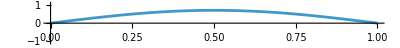

```mathematica
Plot[exactGuitarStringSolution[1/4,x],{x,0,1},PlotRange->{-1.1,1.1},AspectRatio->0.1]
```

### Animating the Exact Solution

```mathematica
Animate[Plot[exactGuitarStringSolution[t,x],{x,0,1},PlotRange->{Automatic,{-1.1,1.1}},AspectRatio->0.1],{t,0,10},DefaultDuration->10,AnimationRunning->False]
```

### Changing the Mode

Try changing the mode to some other number, like 3, and see what the second harmonic looks like.

### Completely Different Initial Conditions

When a guitar string is plucked with something sharp, we can imagine that instead of an initial shape looking like,

z(0,x)=amplitude sin(mπx)

instead we have, if 0<x<b,

z(0,x)=amplitude x/b

and if b<x<length,

z(0,x)=amplitude(length-x)/(length-b)

Using Module[] with {b=1/4}, define a function g[x] that is the right-hand side, taking into account the differing behavior when x<b vs. x>b:

```mathematica
g[x_]:=Module[{b=1/4},amplitude If[x<b,x/b,(length-x)/(length-b)]]
```

Plot your function:

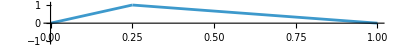

```mathematica
Plot[g[x],{x,0,1},AspectRatio->0.1,PlotRange->{Automatic,{-1.1,1.1}}]
```

Does that look like the way a pick might stretch the string (near the bridge or the sound hole) just before it lets it go?

```mathematica
numericalGuitarStringProblem=Module[{v0=1},{Derivative[2,0][z][t,x]==v0^2 Derivative[0,2][z][t,x],z[t,0]==0, z[t,length]==0,z[0,x]==g[x],Derivative[1,0][z][0,x]==0}];
```

Because of the sharpness of the kink in the string, Mathematica is going to warn us that it actually has considerably difficulty getting a precise solution. Don’t worry it will be pretty good.

```mathematica
numericalGuitarStringSolutionRule=NDSolve[numericalGuitarStringProblem,z,{t,0,1},{x,0,1}][[1]]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

{z^(2,0)[t,x]==z^(0,2)[t,x],z[t,0]==0,z[t,1]==0,z[0,x]==g[x],z^(1,0)[0,x]==0}

Convert the rule to a function:

```mathematica
numericalGuitarStringSolution[t_,x_]=z[t,x]/.numericalGuitarStringSolutionRule
```

ReplaceAll::reps: {numericalGuitarStringSolutionRule} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

z[t,x]/.numericalGuitarStringSolutionRule

### Plotting the Numerical Solution at t=1/4

```mathematica
Plot[exactGuitarStringSolution[1/4,x],{x,0,1},PlotRange->{-1.1,1.1},AspectRatio->0.1]
```

-Graphics-